```mathematica
<<"/home/iubuntu/Descargas/github/caso1/RRT/RandomData.m"
```

```mathematica
lambda=100;
mu=110;
ro=lambda/mu;
nmax=10000;
```

Apartado 1: Generador de números aleatorios

Este apartado se omite porque estamos añadiendo la función RandomData.m, que nos da un generador de números aleatorios.

Apartado 2: Distribucion uniforme

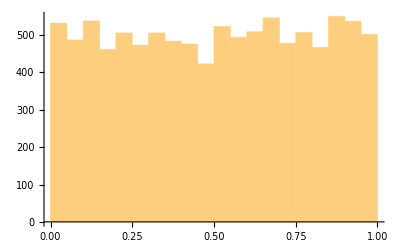

```mathematica
histuniform= Table[RandomData[],{i,nmax}];
Histogram[histuniform]
```

Apartado 3: Numeros aleatorios con randomExp

El array InterArr es un array que almacena el espacio de tiempo que hay entre las llegadas de los paquetes. Estos espacios de tiempo siguen una distribución aleatoria exponencial con tiempo entre llegadas 1/lambda. Este array NO representa el tiempo absoluto en el que llega cada paquete, solo la diferencia entre la llegada de un paquete y el anterior.

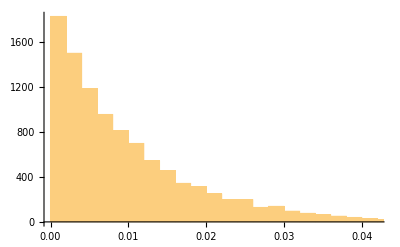

```mathematica
InterArr= Table[RandomExp[lambda],nmax];
Histogram[InterArr]
```

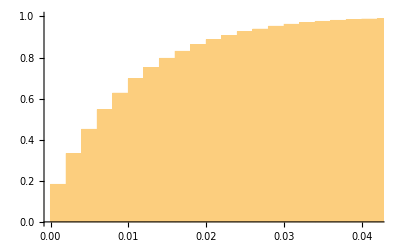

```mathematica
Histogram[InterArr, 50,"CDF"]
```

# PARTE 2

Apartado 4

Para hacer funciones: P.ej, acumular arrivals (sumar una con la anterior)

```mathematica
Arriv=Accumulate[InterArr];
```

```mathematica
ServiceTime=Table[RandomExp[mu],nmax];
```

La siguiente funcion lo que hace es recibir los tiempos de llegada (en tiempo total, no en diferencia entre paquetes) y de servicio (tiempo que tarda en servirse cada paquete) de la cola.  Se analiza paquete a paquete para conseguir los tiempos en los que se estan sirviendo los paquetes.

```mathematica
FifoSchedulling[arrivals_,service_]:=Module[{n,checkTime},n=1;checkTime=arrivals[[1]];
(If[checkTime≥#,checkTime+=service[[n++]],checkTime=#+service[[n++]]])&/@arrivals]
```

```mathematica
DeparturesTime=FifoSchedulling[Arriv,ServiceTime];
```

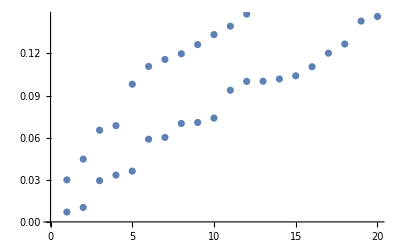

```mathematica
Show[ListPlot[Arriv[[1;;20]]],ListPlot[DeparturesTime[[1;;20]]]]
```

```mathematica
Manipulate[ListPlot[{Arriv[[origin;;origin+width]],DeparturesTime[[origin;;origin+width]]}],{origin,1,1000-width,1},{width,10,40,1}]
```

La siguiente función es para hacer la escalera (mismas gráficas pero los puntos unidos por líneas):

```mathematica
PointStair[lst_]:=Module[{n=0,lastTime=0},Flatten[Map[({{lastTime,n},{lastTime=#,n++}})&,lst],1]]
```

```mathematica
Manipulate[ListLinePlot[{PointStair[Arriv[[1;;width]]],PointStair[DeparturesTime[[1;;width]]]}],{width,10,40,1}]
```

Otra opcion (usando funcion del Mathematica) podría ser la siguiente función. Esto es solo un ejemplo, pero podría sustituirse por las funciones ListLinePlot y PointStair de arriba.

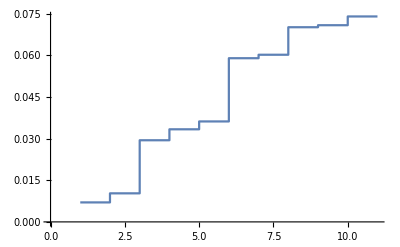

```mathematica
ListStepPlot[Arriv[[1;;10]]]
```

Para mostrar las gráficas de montañas (Numero de usuarios en el sistema)

```mathematica
ArrivalsEvent[lst_]:=Map[{#,1}&,lst];
```

```mathematica
DepartureEvents[lst_]:=Map[{#,-1}&,lst];
```

```mathematica
DrawMontain[lst_]:=Module[{n=0,lastTime=0},
Flatten[
Map[{{lastTime,n},{lastTime=#[[1]],
If[#[[2]]==1,n++,n--]}}&,
lst],
1
]]
```

```mathematica
EventList=Sort[Join[ArrivalsEvent[Arriv[[]]],DepartureEvents[DeparturesTime[[]]]]];
```

```mathematica
listStat=DrawMontain[EventList];
```

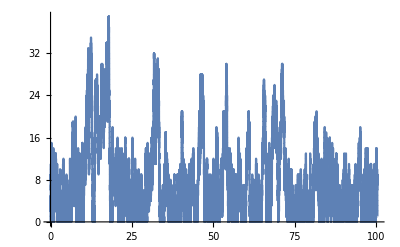

```mathematica
ListLinePlot[listStat]
```

```mathematica
Manipulate[
ListLinePlot[listStat[[1;;width]]],
{width,10,100,1}]
```

## otra cosa que no se que es aun ... codigo de que?

```mathematica
GetStat[lst_,stat_]:=Module[{time=0,lastTime=0},Map[(If[#[[2]]==stat,time+=#[[1]]-lastTime];
lastTime=#[[1]])&,lst];time]
```

```mathematica
ProbTotal[lst_,numest_]:=Module[{estados=Table[i,{i,0,numest,1}]},Map[(GetStat[lst,#]/(lst[[Length[lst]]][[1]]-lst[[1]][[1]]))&,estados]]
```

```mathematica
CheckProb[probs_]:=Module[{acum=0},Map[(acum+=#)&,probs];acum]
```

```mathematica
probabilities=ProbTotal[listStat,8];
CheckProb[probabilities]
```

0.661214

Otra funcion que me he montado pero que no funciona aun

ObtainMaxUserConnected[lst_] := 
 Module[{maxValue = 0},
  Map[(If[#[lst[[]]]])];
  maxValue]

ObtainMaxUserConnected[listStat];

Apartado 5

Primeramente calculamos el tiempo medio de espera estimado para unos valores de mu y lambda concreto. He definido una función que calcula la media de tiempo, y luego esa la uso dentro de la función que utiliza los parametros mu, lambda y ro para poder calcular la media de tiempo para esos valores concretos.

```mathematica
GetMeanTime[ArrivalTimes_,DepartureTimes_]:=Module[{acum,i},For[i=0,i<Length[ArrivalTimes],i++;
	acum+=DepartureTimes[[i]]-ArrivalTimes[[i]];];Return[acum/Length[ArrivalTimes]]]
```

```mathematica
MeanTimeOfRo[lambda_,mu_,n_]:=Module[{i,acum},Table[i,{i,0,n,1}];
For[i=1,i<=n,n++,
InterArrTime=Table[RandomExp[lambda],n];
Arriv=Accumulate[InterArrTime];
ServiceTime=Table[RandomExp[mu],n];
DeparturesTime=FifoSchedulling[Arriv,ServiceTime];
acum[[i]]=GetMeanTime[Arriv,DeparturesTime];]Return[acum]];
```

Se compara con la media teórica

```mathematica
teoric=Plot[1/(1-ro),{ro,0,1},AxesOrigin->{0,0},MeanTimeOfRo[lambda,mu,ro]];
```

Plot::nonopt: Options expected (instead of MeanTimeOfRo[lambda,mu,ro]) beyond position 2 in Plot[1/(1-ro),{ro,0,1},AxesOrigin→{0,0},MeanTimeOfRo[lambda,mu,ro]]. An option must be a rule or a list of rules.

Apartado 6